# Avaliação do Campo Crítico em Circuito de 230 kV

## Antonio C. S. Lima

Este documento apresenta o cálculo do campo crítico nos condutores para um circuito de 230kV 
Não comtempla os cabos PR

## Inicialização

```mathematica
SetDirectory[NotebookDirectory[]]
(*SetDirectory["B:\\otlin"]*)
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
SetOptions[{Plot,LogPlot,LogLinearPlot,LogLogPlot},BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,PlotStyle-> Thick,
Axes-> False,Frame-> True];
```

```mathematica
dadoscond=Import["condcompleta.txt","Table"];
camp=Import["campos.txt","CSV"];
```

## Variáveis obtidas do programa de otimização dos condutores

```mathematica
nfase=3;
ns=2;
npr=2;
ncond=IntegerPart[ns*nfase+npr]
```

8

### Dados do Meio

#### Ar

```mathematica
μo=4.0*Pi*10^-7;
ϵo=8.854 10^-12;
```

#### Solo

```mathematica
σearth=1.0 10^-3;                                 (* ⟹ Condutividade do Solo ⟸ *)
```

### Dados do condutor

```mathematica
Nome=ToUpperCase["rail"];
```

```mathematica
pos=Module[{posicao},posicao=If[NumberQ[Position[dadoscond,Nome][[1,1]]],Position[dadoscond,Nome][[1,1]],1];If[NumberQ[Position[dadoscond,Nome][[1,1]]],,Print["O condutor especificado não exite na tabela, verifique o nome digitado. Para não ocorrer erros nos cálculos foram utilizados os valores do condutor Owl"]];Return[posicao]];

{nome,MCM,NAl,DAl,NACO,DACO,secAl,secACO,Dcond,DALMA,PesoAl,PesoACO,Massa,CargaRupturaClasseA,CargaRupturaClasseB,Ampacidade,RMG,ResCC,ResAC,Xind,Xcap}=dadoscond[[pos]];

Table[Print[i,")  ",camp[[i,1]], " = ",dadoscond[[pos,i]]],{i,1,Length[camp]}];
```

Return[45]

1)  Nome comercial = RAIL

2)  Bitola (MCM) = 954

3)  Num. de Fios de Al. = 45

4)  Diâmetro dos Fios de Al. (mm) = 3.698

5)  Num. de Fios de Aço = 7

6)  Diâmetro dos Fios de Aço (mm) = 2.466

7)  Seção transversal de Al (mm^2) = 483.32

8)  Seção transversal do cond. (mm^2) = 516.8

9)  Diâmetro do cond. (mm) = 29.59

10)  Diâmetro da Alma de Aço (mm) = 7.4

11)  Peso Nominal do Al (aprox.) (kg/km) = 1339.1

12)  Peso nominal do Aço (aprox.) (kg/km) = 261.1

13)  Massa (aprox.) (kg/km) = 1600.2

14)  Carga de ruptura (Classe A) (kgf) = 11764

15)  Carga de ruptura (Classe B) (kgf) = 11535

16)  Ampacidade (A) = 970

17)  Raio médio geométrico (m) = 0.01174

18)  Resistência elétrica máxima CC a 20.baC (Ohm/km) = 0.06

19)  Resistência elétrica máxima CA @ 60 Hz e 75.baC (Ohm/km) = 0.073

20)  Reatância indutiva (Ohm/km) = 0.3352

21)  Reatância capacitiva (Mohm/km) = 0.2011

### Dados dos Condutores

```mathematica
r0=(dadoscond[[pos,10]]/2)*10^-3;   (* ⟹ [m] ⟸ *)
r1=(dadoscond[[pos,9]]/2)*10^-3;

ρAl=0.028264;    (* resistividade ⟹ Ω × mm^2/ m ⟸ *)
ρAlmetro=0.028264*10^-6;    (* ⟹ Ω × m ⟸ *)

Rdcϕ=(dadoscond[[pos,18]])*10^-3;  (* ⟹ [Ω/m] ⟸⟹ @ 20^o ⟸*)
ρϕ=Rdcϕ*Pi*(r1^2-r0^2);

σϕ=(1/ρAlmetro)*(dadoscond[[pos,3]]*(dadoscond[[pos,4]]*10^-3/2)^2)/(r1^2-r0^2);
```

```mathematica
svao=0.45; (* comprimento do vão em [km] *)
T=dadoscond[[pos,15]];
W=dadoscond[[pos,13]];
H=0.24*T;
Ccat=H/W;
(*flecha em metro
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)*)
flechacond=1000*Ccat*(Cosh[svao/(2*Ccat)]-1)
```

14.6519

### Dados dos Cabos PR

```mathematica
rpr=4.57*10^-3; (* [m] *)

Rdcpr=4.19*10^-3;

ρpr=Rdcpr*Pi*rpr^2;

σpr=1/ρpr;

μpr=80*μo;
```

```mathematica
Tpr=6980; (*{kgf]*)
Wpr=410; (*[kg/km]*)
Hpr=0.25*Tpr;
Ccatpr=Hpr/Wpr;
(*flecha em metro*)
flechapr=1000*Ccatpr*(Cosh[svao/(2*Ccatpr)]-1)
```

5.94873

#### Lista de raios dos condutores

```mathematica
r=Join[Table[r1,{ncond-npr}],Table[rpr,{npr}]];
```

## Coordenadas dos condutores

```mathematica
varx=Array[ToExpression[StringJoin["coorx",ToString[#]]]&,ncond];
vary=Array[ToExpression[StringJoin["coory",ToString[#]]]&,ncond];
```

```mathematica
b=.457; (* espacamento entre os feixes *)
h=14.651852276415907; (*flecha dos condutores *)
xc={ -7.85-b/2, -7.85+b/2,-b/2,b/2,7.85-b/2, 7.86+b/2, -7,7};
yc={7.5+h,7.5+h,7.5+h,7.5+h,7.5+h,7.5+h,7.5+h+5.3,7.5+h+5.3};
```

```mathematica
yc
```

{22.1519,22.1519,22.1519,22.1519,22.1519,22.1519,27.4519,27.4519}

```mathematica
yini2=Table[If[i<=ncond-npr,yc[[i]]-flechacond,yc[[i]]-flechapr],{i,ncond}];
```

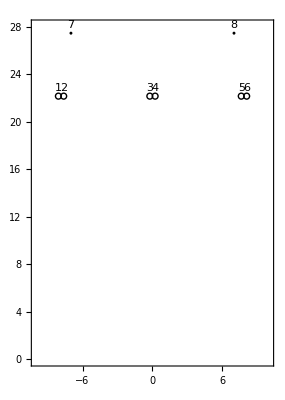

```mathematica
mostra=Table[If[i≤ Length[xc]-2,
Circle[{xc[[i]],yc[[i]]},0.25],
Disk[{xc[[i]],yc[[i]]},.125]],
{i,1,Length[xc]}];
num=Table[Text[i,{xc[[i]],.65+yc[[i]]}],{i,1,8}];

Show[{Graphics[num],Graphics[mostra]},Frame-> True,PlotRange->{{-10,10},{0,28.0}}]
```

## Definição da Funçao Objetivo e Otimização

### Dados

```mathematica
(*== Tensão Fase-Neutro (kV) ==*)
NU1=230./Sqrt[3]; 

(*== Potência Característica (MW) ==*)
NPc=300;                     

nfase=3;

(* Densidade de Corrente *)
NJc=0.82;                     

(* Fator de Preenchimento *)
Npreen=0.7;                

(* Fator de Utilização *)
Nku= 0.95;                    

(* Altura  [m] *)
Nh=100;

(* temperatura do Cond [°C]*)

Ntemp=60;

(* temperatura do Ar [°C]*)

NtempAr=40;

(* Fator de Superfície *)
Nm=0.82;                       

(* Tolerância *)
Ntol=3*10^-2;
```

### Densidade Relativa e Campo Crítico

```mathematica
δ1[h_,t_]:=0.28924*(1013*Exp[-0.116*(h/1000)])/(273+t);
(* Apostila do Portela *)
```

```mathematica
EcrPortela[r_,h_,t_,m_]:=Module[{Ec,Ecm,Ecr,A1,A0,raux},
A0=829.7;
A1=781.53;
Ec=2.4381;
Ecm=Ecr/(m*δ1[h,t]);
raux=r*δ1[h,t];

(*resultado é dado em MV/m e em valor Pico*)

Ecr/.FindRoot[-A0*(Ecm/Ec-1)^2+A1*Ecm*(Ecm/Ec-1-Log[Ecm/Ec])==1/raux,{Ecr,Ec}]];
```

```mathematica
EcrCond=EcrPortela[r1,Nh,Ntemp,Nm]*10/Sqrt[2];
EcrPr=EcrPortela[rpr,Nh,NtempAr,Nm]*10/Sqrt[2];
Print["Campo Elétrico Crítico Cond"," = ",EcrCond," kV/cm"];
Print["Campo Elétrico Crítico PR"," = ",EcrPr," kV/cm"]
```

Campo Elétrico Crítico Cond = 19.0102 kV/cm

Campo Elétrico Crítico PR = 24.3613 kV/cm

## Campo Elétrico Superficial

### Determinação da Matriz de Potenciais de Maxwell (Númerica e Simbólica)

```mathematica
PNum[xx1_List?(Union[Map[NumberQ,#]][[1]]&),yy1_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{pp},
pp=1/(2*Pi*ϵo)*Log[Table[If[i==j,2*yy1[[i]]/r[[i]],(Sqrt[(yy1[[i]]+yy1[[j]])^2+(xx1[[i]]-xx1[[j]])^2]/Sqrt[(yy1[[i]]-yy1[[j]])^2+(xx1[[i]]-xx1[[j]])^2])],{i,1,ncond},{j,1,ncond}]];Return[pp]];
```

```mathematica
PSym[xx2_List,yy2_List]:=Module[{pp},
pp=1/(2*Pi*ϵo)*Log[Table[If[i==j,2*yy2[[i]]/r[[i]],(Sqrt[(yy2[[i]]+yy2[[j]])^2+(xx2[[i]]-xx2[[j]])^2]/Sqrt[(yy2[[i]]-yy2[[j]])^2+(xx2[[i]]-xx2[[j]])^2])],{i,1,ncond},{j,1,ncond}]];Return[pp]];
```

#### Vetor de tensões, considerando os cabos PR aterrados em todas as torres

```mathematica
MU=(NU1*10^3)*Join[Flatten[Table[Exp[-(ⅈ*2*π/nfase)*#],{ns}]&/@Range[0,nfase-1]],Table[0,{npr}]]
```

{132791.,132791.,-66395.3-115000. ⅈ,-66395.3-115000. ⅈ,-66395.3+115000. ⅈ,-66395.3+115000. ⅈ,0.,0.}

#### Calculo das cargas nos condutores

```mathematica
qtotal[xx3_List?(Union[Map[NumberQ,#]][[1]]&),yy3_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{q},
(*as tensões devem estar em Volts *)
q=Inverse[PSym[xx3,yy3]].MU; Return[q]]
```

#### Campos Superficiais Máximos

```mathematica
Esupmax[xx4_List?(Union[Map[NumberQ,#]][[1]]&),yy4_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{Nq,C00,campos,camposmax,camposmaxmax,γ,ang},

ang[i_,j_]:=Module[{},If[j<=ncond,If[i==j,0,ArcTan[xx4[[j]]-xx4[[i]],yy4[[j]]-yy4[[i]]]],If[i==j,-π/2,ArcTan[xx4[[j-ncond]]-xx4[[i]],yy4[[j-ncond]]+yy4[[i]]]]]];

Nq=qtotal[xx4,yy4];

C00=Table[(Nq[[i]]/(2*π*ϵo*r[[i]])),{i,Length[Nq]}];

campos=Table[C00[[i]]+Sum[Sum[If[k==i,0,If[k<=ncond,-2*Nq[[i]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yy4[[i]]-yy4[[k]])^2+(xx4[[i]]-xx4[[k]])^2])^h*Cos[γ-ang[i,k]],2*Nq[[k-ncond]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yy4[[i]]+yy4[[k-ncond]])^2+(xx4[[i]]-xx4[[k-ncond]])^2])^h*Cos[γ-ang[i,k]]]],{k,1,2*ncond}],{h,1,2}],{i,ncond}];

 camposmax=Table[FindMinimum[-Abs[campos[[i]]],{γ,0,2*π}],{i,Length[campos]}];

camposmaxmax=Max[-camposmax[[All,1]]]*10^-5;Return[-camposmax[[All,1]]*10^-5]]
```

```mathematica
EsupmaxInd[posi_,xx5_List?(Union[Map[NumberQ,#]][[1]]&)]:=Block[{xEmax,yEmax,ytemp,pts,Nq,C00,campos,camposmax,camposmaxmax,γ,ang},

pts=Thread[varsym->xx5];

xEmax=varx/.pts;

(*O campo é crítico no meio do vão*)

ytemp=vary/.pts;

yEmax=Table[If[i<=ncond-npr,ytemp[[i]]-flechacond,ytemp[[i]]-flechapr],{i,ncond}];

ang[i_,j_]:=Module[{},If[j<=ncond,If[i==j,0,ArcTan[xEmax[[j]]-xEmax[[i]],yEmax[[j]]-yEmax[[i]]]],If[i==j,-π/2,ArcTan[xEmax[[j-ncond]]-xEmax[[i]],yEmax[[j-ncond]]+yEmax[[i]]]]]];

Nq=qtotal[xEmax,yEmax];

C00=Table[(Nq[[i]]/(2*π*ϵo*r[[i]])),{i,Length[Nq]}];

campos=Table[C00[[i]]+Sum[Sum[If[k==i,0,If[k<=ncond,-2*Nq[[i]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yEmax[[i]]-yEmax[[k]])^2+(xEmax[[i]]-xEmax[[k]])^2])^h*Cos[γ-ang[i,k]],2*Nq[[k-ncond]]/(2*π*ϵo*r[[i]])*(r[[i]]/Sqrt[(yEmax[[i]]+yEmax[[k-ncond]])^2+(xEmax[[i]]-xEmax[[k-ncond]])^2])^h*Cos[γ-ang[i,k]]]],{k,1,2*ncond}],{h,1,2}],{i,ncond}];

 camposmax=Table[FindMinimum[-Abs[campos[[i]]],{γ,0,2*π}],{i,Length[campos]}];
Return[-camposmax[[posi,1]]*10^-5]]
```

```mathematica
yini2=Table[If[i<=ncond-npr,yc[[i]]-flechacond,yc[[i]]-flechapr],{i,ncond}];
```

```mathematica
Esupmaxini=Esupmax[xc,yini2];
Ecrtodos=Table[If[i<=ncond-npr,EcrCond,EcrPr],{i,ncond}];

fatorEc=Esupmaxini[[#]]/Ecrtodos[[#]]&/@Range[ncond];
```

```mathematica
Esolo[xsolo_,ysolo_,xx_List?(Union[Map[NumberQ,#]][[1]]&),yy_List?(Union[Map[NumberQ,#]][[1]]&)]:=Module[{Nq,Esolo},
Nq=qtotal[xx,yy];

Esolo=Sum[(Nq[[k]]/(2*π*ϵo))*((xsolo-xx[[k]])*(1/((xsolo-xx[[k]])^2+(ysolo-yy[[k]])^2)-1/((xsolo-xx[[k]])^2+(ysolo+yy[[k]])^2))+ⅈ*((ysolo-yy[[k]])/((xsolo-xx[[k]])^2+(ysolo-yy[[k]])^2)-(ysolo+yy[[k]])/((xsolo-xx[[k]])^2+(ysolo+yy[[k]])^2))),{k,Length[xx]}];

Return[Esolo]]
```

```mathematica
TableForm[Transpose[{Join[{"N°"},Range[Length[varx]]],Join[{"Emax (kV/cm)"},Esupmaxini],Join[{"Emax/Ec"},fatorEc]}]]
```

N° | Emax (kV/cm) | Emax/Ec
1 | 10.3607 | 0.545006
2 | 10.2805 | 0.540787
3 | 10.9251 | 0.574695
4 | 10.9254 | 0.57471
5 | 10.2884 | 0.541202
6 | 10.3664 | 0.545306
7 | 1.67641 | 0.0688146
8 | 1.68676 | 0.0692393

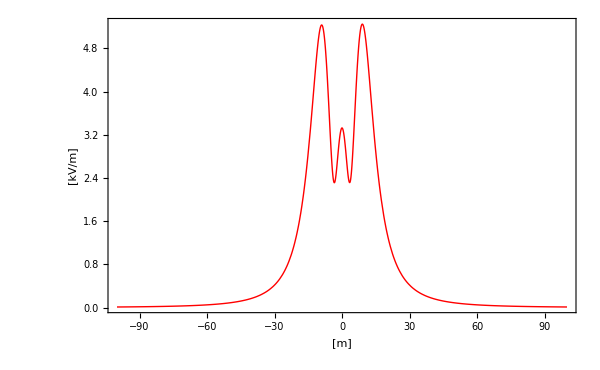

```mathematica
CampoSolo=Plot[Abs[Esolo[x,1,xc,yini2]]/1000,{x,-100,100},
PlotRange->{{-100,100},All},
PlotStyle->{RGBColor[1,0,0],AbsoluteThickness[1]},
Axes->False,
FrameLabel->{"[m]", "[kV/m]"}]
```